```mathematica
Subscript[x, ank][dt] = Subscript[x, ank][0] + s
```

x_ank(0)+s

```mathematica
dt[s_] = a + b * s
```

a+b s

```mathematica
Subscript[E, x][t_] = 1/2*x'[t]^2 - 1/2 * (x[t] - Subscript[x, ank][t])^2
```

1/2 (1/2 ⅇ^-t (2 ⅇ^(2 t) x0+2 ⅇ^(2 t) xd0)-1/2 ⅇ^-t (ⅇ^(2 t) x0+ⅇ^(2 t) xd0+x0-xd0))^2-1/2 (1/2 ⅇ^-t (ⅇ^(2 t) x0+ⅇ^(2 t) xd0+x0-xd0)-x_ank(t))^2

```mathematica
Subscript[E, x][dt[s]]
```

```mathematica
1/2 (1/2 ⅇ^(-a-b s) (2 x0 ⅇ^(2 (a+b s))+2 xd0 ⅇ^(2 (a+b s)))-1/2 ⅇ^(-a-b s) (x0 ⅇ^(2 (a+b s))+xd0 ⅇ^(2 (a+b s))+x0-xd0))^2-1/2 (1/2 ⅇ^(-a-b s) (x0 ⅇ^(2 (a+b s))+xd0 ⅇ^(2 (a+b s))+x0-xd0)-Subscript[x, ank](a+b s))^2
```

```mathematica
N[Subscript[E, x][dt[0]]]
```

0.5 (0.5 2.71828^(-1. a) (2. 2.71828^(2. a) x0+2. 2.71828^(2. a) xd0)-0.5 2.71828^(-1. a) (2.71828^(2. a) x0+2.71828^(2. a) xd0+x0-1. xd0))^2-0.5 (0.5 2.71828^(-1. a) (2.71828^(2. a) x0+2.71828^(2. a) xd0+x0-1. xd0)-1. x_ank(a))^2

```mathematica
solution = DSolve[{y''[t]==y[t]-ank_0,y[0]==x0,y'[0]==xd0},y[t],t]
```

{{y(t)→1/2 ⅇ^-t (ⅇ^(2 t) x0+ⅇ^(2 t) xd0+x0-xd0)}}

```mathematica
x[t_] = y[t] /.solution[[1]]
```

1/2 ⅇ^-t (ⅇ^(2 t) x0+ⅇ^(2 t) xd0+x0-xd0)

```mathematica
s2 = Sinh[2]
```

sinh(2)

```mathematica
c2 = Cosh[2]
```

3.7622

```mathematica
w = 1
```

1

```mathematica
N[w s2/ 2 * s2 - w c2/2 * c2 + ra2f]
```

4.5

```mathematica
ra2f = 5
```

5

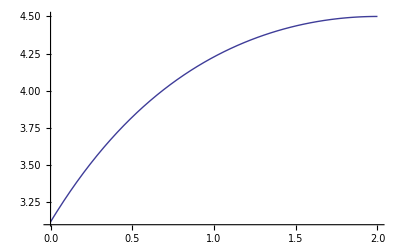

```mathematica
Plot[w s2/2 * Sinh[t] - w c2 / 2 * Cosh[t] + ra2f, {t, 0, 2}]
```

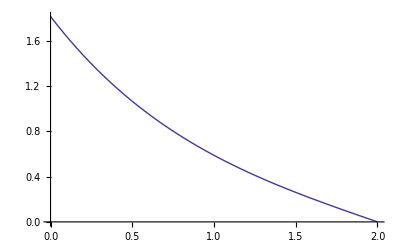

```mathematica
Plot[w s2 /2 * Cosh[t] - w c2/ 2 * Sinh[t], {t, 0, 2}]
```

```mathematica
N[Cosh[0]]
```

1.

```mathematica
s1 = Sinh[1]
```

sinh(1)

```mathematica
c1 = Cosh[1]
```

cosh(1)

```mathematica
(s1 (1-2c1-c2))^2 / (c1(2c1-c2-1))^2
```

7.06235

```mathematica
N[2*s2]
```

7.25372

```mathematica
r[_t0] = r0
```

r0

```mathematica
rd[_t0] = rd0
```

rd0

```mathematica
ra1f = r[t0] + Sqrt[rd[t0]^2 - w^2/2 (Cosh[t2 - t1] - 5/2)]
```

r(t0)+√((rd(t0))^2-1/2 w^2 (cosh(t1-t2)-5/2))

```mathematica
E[_t0] = 1/2(rd[t0])^2 - 1/2(r[t0] - ra1f)^2
```

Set::write: Tag TraditionalForm`ⅇ in TraditionalForm`ⅇ(_t0) is Protected.

1/2 (1/2 w^2 (cosh(t1-t2)-5/2)-(rd(t0))^2)+(rd(t0))^2/2

```mathematica
Simplify[rd[t0]^2/2+1/2 (1/2 w^2 (-5/2+Cosh[t1-t2])-rd[t0]^2)]
```

1/8 w^2 (2 cosh(t1-t2)-5)

```mathematica
Simplify[2Cosh[x] - Cosh[2x]]
```

2 cosh(x)-cosh(2 x)

```mathematica
Simplify[Cosh[2x]/Cosh[x]]
```

cosh(2 x) sech(x)

```mathematica
Solve[y==l * 1/Sinh[t] (2 - c21 + Cosh[t]^2(c21-2) + Sinh[t]Cosh[t]s21), {t}]
```

{{t→ConditionalExpression[log((y-√(c21^2 l^2-4 c21 l^2-l^2 s21^2+4 l^2+y^2))/(c21 l+l s21-2 l))+2 ⅈ π c_1,c_1∈ℤ]},{t→ConditionalExpression[log((√(c21^2 l^2-4 c21 l^2-l^2 s21^2+4 l^2+y^2)+y)/(c21 l+l s21-2 l))+2 ⅈ π c_1,c_1∈ℤ]}}

```mathematica
Last[%4]
```

{t→ConditionalExpression[log((√(c21^2 l^2-4 c21 l^2-l^2 s21^2+4 l^2+y^2)+y)/(c21 l+l s21-2 l))+2 ⅈ π c_1,c_1∈ℤ]}

```mathematica
t/.{t->ConditionalExpression[2 ⅈ π C[1]+Log[(y+√(4 l^2-4 c21 l^2+c21^2 l^2-l^2 s21^2+y^2))/(-2 l+c21 l+l s21)],C[1]∈Integers]}
```

ConditionalExpression[log((√(c21^2 l^2-4 c21 l^2-l^2 s21^2+4 l^2+y^2)+y)/(c21 l+l s21-2 l))+2 ⅈ π c_1,c_1∈ℤ]

```mathematica
t1 = Log[(y+√(4 l^2-4 c21 l^2+c21^2 l^2-l^2 s21^2+y^2))/(-2 l+c21 l+l s21)]
```

log((√(c21^2 l^2-4 c21 l^2-l^2 s21^2+4 l^2+y^2)+y)/(c21 l+l s21-2 l))

```mathematica
Simplify[l(1-2Cosh[t1] + Cosh[t1]c21 + Sinh[t1]s21)]
```

(l (√(l^2 (c21^2-4 c21-s21^2+4)+y^2)+y)+y (√(l^2 (c21^2-4 c21-s21^2+4)+y^2)+y)+l^2 (c21^2-4 c21-s21^2+4))/(√(l^2 (c21^2-4 c21-s21^2+4)+y^2)+y)

```mathematica
Simplify[1/2*y^2 -1/2(l(1-2Cosh[t1] + Cosh[t1]c21 + Sinh[t1]s21))^2]
```

-(l (2 l^2 (c21^2-4 c21-s21^2+4) (√(l^2 (c21^2-4 c21-s21^2+4)+y^2)+2 y)+2 l y (c21^2-4 c21-s21^2+5) (√(l^2 (c21^2-4 c21-s21^2+4)+y^2)+y)+4 y^2 (√(l^2 (c21^2-4 c21-s21^2+4)+y^2)+y)+l^3 (c21^4-8 c21^3+c21^2 (25-2 s21^2)+4 c21 (2 s21^2-9)+s21^4-9 s21^2+20)))/(2 (√(l^2 (c21^2-4 c21-s21^2+4)+y^2)+y)^2)

```mathematica
Simplify[Cosh[ArcSinh[t]]]
```

√(t^2+1)

```mathematica
Manipulate[Plot[rd Sinh[t] + r Cosh[t], {t, 0, 1}], {rd, -1, 4}, {r, -1, 1}]
```